# Risanje logota in transformacije

Opis projekta: S funkcijami izrišemo logo in nato delamo različne transformacije z njim. Možne so tranformacije, ki se tičejo funkcij, kar so premiki in raztegi.

# 1. Funkcije

Funkcija f : A → B  je v matematiki preslikava, ki vsakemu elementu množice A priredi natanko en element množice B.
Če definiramo funkcijo  f : a → b, je a podatek ali original, b pa je funkcijska vrednost oziroma rezultat ali slika. Funkcijsko zvezo lahko krajše zapišemo  b = f(a).

Množica A je množica vseh podatkov, na katerih izvajamo funkcijo f; torej množica vseh podatkov, za katere je funkcija definirana. Imenujemo jo tudi definicijsko območje funkcije f. Oznaka: D_f
Množico vseh funkcijskih vrednosti, ki jih pri tem dobimo, imenujemo zaloga vrednosti funkcije f. Oznaka: Z_f
Zaloga vrednosti je lahko enaka množici B, lahko pa je tudi njena prava podmnožica.

Graf funkcije je množica točk (x, y), za katere velja med koordinatama zveza y = f (x), torej: G_f = {(x, y); y = f(x)}

Enačbo y = f (x) imenujemo tudi enačba grafa funkcije.
Zgled: Graf funkcije f (x) = x^3 − 4x   (to je množica točk, za katere velja enačba y = x^3 − 4x):

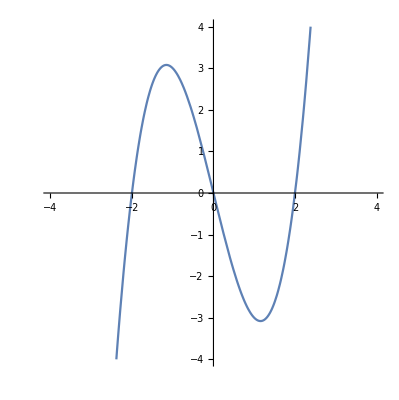

```mathematica
Plot[y /. Solve[y==x^3−4x ], {x,-4,4},PlotRange->{-4,4},AspectRatio->Automatic]
```

# 2. Risanje logota

Vsaka funkcija predstavla neko krivuljo. Potrebno je samo najditi pravo krivuljo in če potrebno, jo omejiti. Za našo nalogo bomo izrisali logo batman - a. 
(predogled)

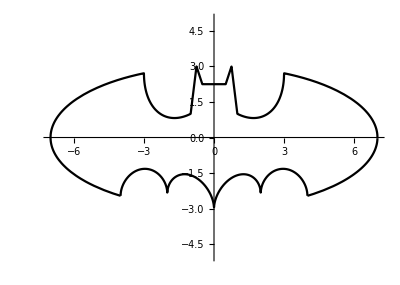

```mathematica
Show[bat1,bat2,bat3]
```

1. Za robove kril moramo pravilno omejiti elipso z enačbo (x/7)^2 + (y/3)^2 - 1 = 0, ki zgleda takole:

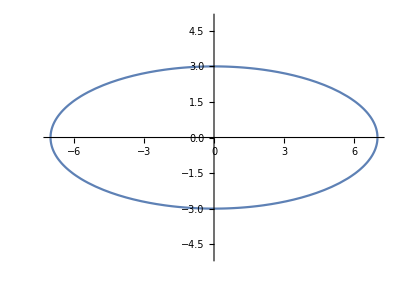

```mathematica
Plot[y /. Solve[(x/7)^2 + (y/3)^2 - 1 == 0], {x,-8,8},PlotRange->{-5,5},AspectRatio->Automatic]
```

Sedaj to elipso še omejimo na intervalu x ∈ (-3, 3).

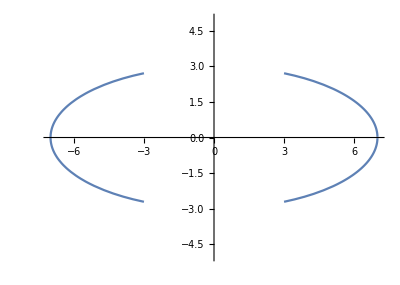

```mathematica
Plot[y /. Solve[(x/7)^2 + (y/3)^2 - 1 == 0], {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic, RegionFunction->Function[{x},Abs[x]>3]]
```

Razdelimo na dele, ker bo naprej lažje delati.
Spodnja del: -3*√(1-(x/7)^2)

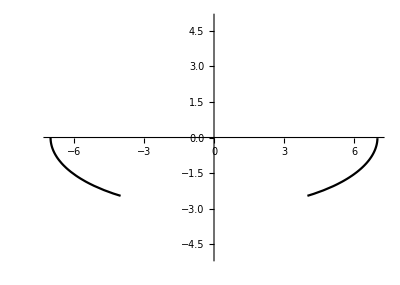

```mathematica
f1 = -3*√(1-(x/7)^2);
bat1 = Plot[f1, {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic, RegionFunction->Function[{x},Abs[x]>4],PlotStyle->Black]
```

Enačba za zgornji del: 3*√(1-(x/7)^2)
Enačbi sta med sabo enaki, razlikujeta se samo v predznaku.

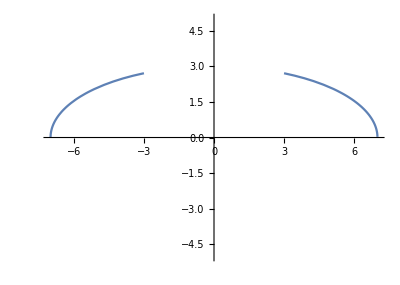

```mathematica
Krivulja1 = Plot[3*√(1-(x/7)^2), {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic, RegionFunction->Function[{x},Abs[x]>3]]
```

2. Spodnji del kril dobimo, če seštejemo naslednje dve funkciji: y =|x/2|−(3 √33−7)/112 x^2−3 in y=√(1−(||x|−2|−1)^2)

Tako zgleda: y =|x/2|−(3 √33−7)/112 x^2−3

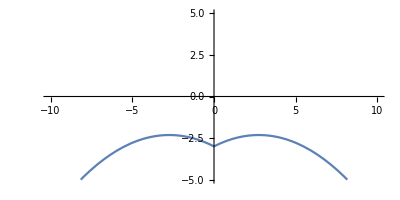

```mathematica
Plot[y /. Solve[y ==Abs[x/2]−(3 √33−7)/112 x^2−3], {x,-10,10},PlotRange->{-5,5},AspectRatio->Automatic]
```

Tako zgleda:y=√(1−(||x|−2|−1)^2)

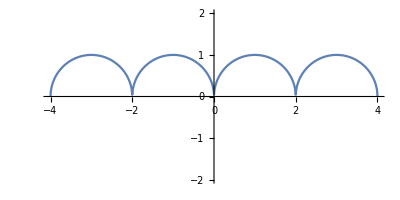

```mathematica
Plot[y /. Solve[y==√(1−(Abs[Abs[x]−2]−1)^2)], {x,-10,10},PlotRange->{-2,2},AspectRatio->Automatic]
```

Torej skupna enačba y =|x/2|−(3 √33−7)/112 x^2−3+√(1−(||x|−2|−1)^2)

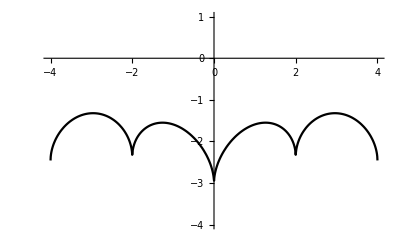

```mathematica
f2 = Abs[x/2]−(3 √33−7)/112 x^2−3+√(1−(Abs[Abs[x]−2]−1)^2);
bat2 =Plot[f2, {x,-10,10},PlotRange->{-4,1},AspectRatio->Automatic,PlotStyle->Black]
```

3. Sedaj bomo naredili glavo, ki je sestavljena iz naslednjih treh krivulj oziroma ravne premice, ki so omejene.
Prva premica je y =   9 - 8 |x|, omejena sledeče: (0.75 < |x| < 1)

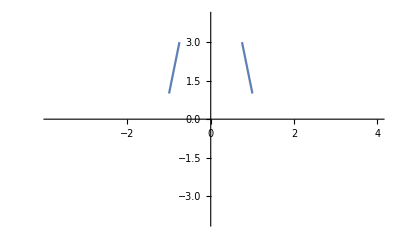

```mathematica
Krivulja2 =Plot[y /. Solve[y==9-8Abs[x]], {x,-4,4},PlotRange->{-4,4},RegionFunction->Function[{x},0.75<Abs[x]<1]]
```

Druga premica y = 3 |x| + 0.75, omejena sledeče:  (0.5 < |x| < 0.75)

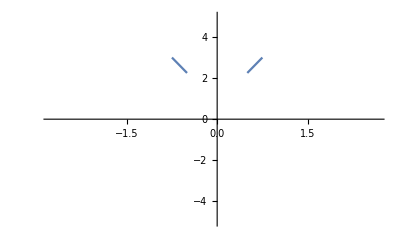

```mathematica
Krivulja3 =Plot[y /. Solve[y==3Abs[x]+0.75],{x,-5,5},PlotRange->{-5,5},RegionFunction->Function[{x},0.5<Abs[x]<0.75]]
```

In še zadnja premica y = 2.25, omejena na intervalu x ∈ (−0.5 < x < 0.5)

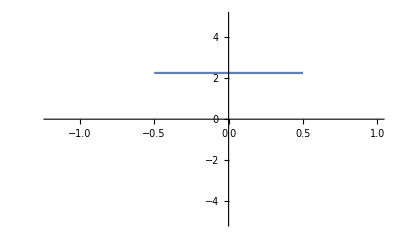

```mathematica
Krivulja4 =Plot[y /. Solve[y==2.25],{x,-5,5},PlotRange->{-5,5},RegionFunction->Function[{x},−0.5<x<0.5]]
```

Če jih sedaj še na enkrat izrišemo, dobimo celotno glavo.

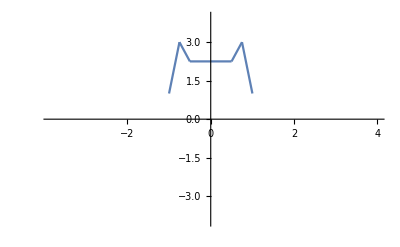

```mathematica
Show[Krivulja2,Krivulja3,Krivulja4]
```

4. Še zadnja komponenta.
 Da dobimo začeten del kril, potrebujemo krivuljo y =(6 √10)/7+(1.5−0.5Abs[x])-((6 √10)/14)√(4-(Abs[x]-1)^2) ,ki jo moramo omejiti na intervalu x ∈ (-1, 1).
 Krivulja:

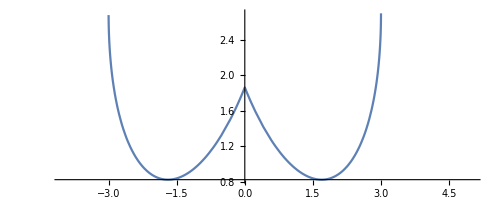

```mathematica
Plot[y /. Solve[y ==(6 √10)/7+(1.5−0.5Abs[x])-((6 √10)/14)√(4-(Abs[x]-1)^2)], {x,-4,5},AspectRatio-> Automatic]
```

Sedaj še omejena:

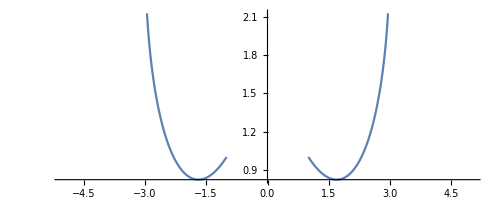

```mathematica
Krivulja5 =Plot[y /. Solve[y ==(6 √10)/7+((3−Abs[x])/2)-((3 √10)/7)√(4-(Abs[x]-1)^2)], {x,-5,5},AspectRatio->Automatic,RegionFunction->Function[{x},Abs[x]>1]]
```

Če damo vse krivluje skupaj dobimo logo. Ampak lahko opazimo, da se nekje pojavijo luknje.

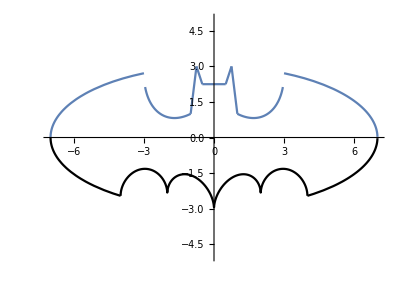

```mathematica
Show[bat1,bat2,Krivulja1,Krivulja2,Krivulja3,Krivulja4,Krivulja5]
```

To popravimo tako, da vzamemo vse formule zgornjih krivulj (krivulje, ki so nad x osjo) in jih damo v skupno funkcijo. Nato še z Unitstepom povežemo dane krivulje. Premice, ki tvorijo glavo, smo preoredili v eno enačbo.

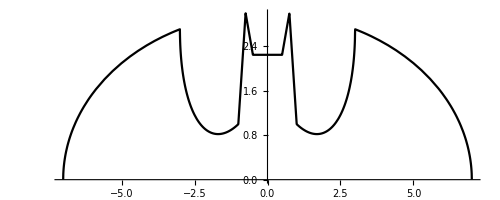

```mathematica
bat3 =Plot[{With[{krila=3*√(1-(x/7)^2),
l=(6 √10)/7+((3+x)/2)-((3 √10)/7)√(4-(Abs[x]-1)^2),
h=(3 (Abs[x-1/2]+Abs[x+1/2]+6)-11 (Abs[x-3/4]+Abs[x+3/4]))/2,

r=(6 √10)/7+((3−x)/2)-((3 √10)/7)√(4-(Abs[x]-1)^2)},krila+(l-krila) UnitStep[x+3]+(h-l) UnitStep[x+1]+(r-h) UnitStep[x-1]+(krila-r) UnitStep[x-3]]},{x,-7,7},AspectRatio->Automatic,PlotStyle->Black]
```

Če sedaj izrišemo popravljeno verzijo dobimo celoten logo.

```mathematica
Show[bat1,bat2,bat3]
```

-Graphics-

# 3. Transformacije

Premiki po y osi

y = f (x) + q
Število q, ki ga prištejemo funkciji, pomeni premik grafa funkcije v smeri osi y za q. 
Pri tem se y koordinata vsake točke na grafu poveča za q (in x koordinata ostane nespremenjena).
Zgled za: f(x) = x^2

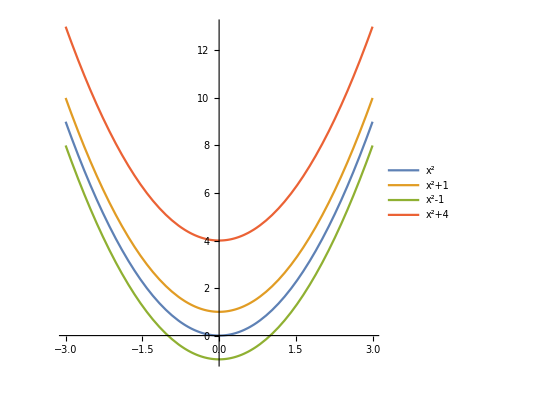

```mathematica
Plot[{x^2,x^2+1,x^2-1,x^2+4},{x,-3,3},PlotLegends->"Expressions",AspectRatio->1]
```

Torej za premik po y osi moramo funkciji samo prišteti oziroma odšteti neko število.
Da si olajšamo delo smo vse zgornje krivulje izrazili z eno funkcijo in ji prištel neko število.

```mathematica
Manipulate[Plot[{With[{w=3 Sqrt[1-(x/7)^2]+q,
l=6/7 Sqrt[10]+(3+x)/2-3/7 Sqrt[10] Sqrt[4-(x+1)^2]+q,
h=(3 (Abs[x-1/2]+Abs[x+1/2]+6)-11 (Abs[x-3/4]+Abs[x+3/4]))/2+q,
r=6/7 Sqrt[10]+(3-x)/2-3/7 Sqrt[10] Sqrt[4-(x-1)^2]+q},
w+(l-w) UnitStep[x+3]+(h-l) UnitStep[x+1]+(r-h) UnitStep[x-1]+(w-r) UnitStep[x-3]],1/2 (3 Sqrt[1-(x/7)^2]+Sqrt[1-(Abs[Abs[x]-2]-1)^2]+Abs[x/2]-((3 Sqrt[33]-7)/112) x^2-3) (Sign[x+4]-Sign[x-4])-3*Sqrt[1-(x/7)^2]+q},{x,-7,7},AspectRatio->Automatic,PlotRange->{-15,15},PlotStyle->Black],{q,-10,10}]
```

y = f (x − p).
Število p, ki ga odštejemo od neodvisne spremenljivke x, pomeni premik grafa funkcije v smeri osi x za p.
Pri tem se x koordinata vsake točke na grafu poveča za p (in y koordinata ostane nespremenjena).
Zgled za: f(x) = x^2

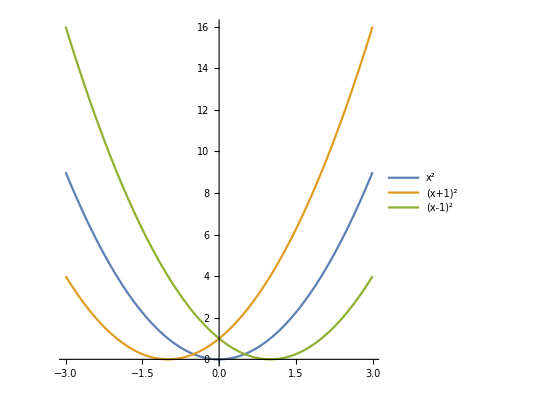

```mathematica
Plot[{x^2,(x+1)^2,(x-1)^2},{x,-3,3},PlotLegends->"Expressions",AspectRatio->1]
```

Premik po x osi.

```mathematica
Manipulate[Plot[{With[{w=3 Sqrt[1-((x+p)/7)^2],
l=6/7 Sqrt[10]+(3+(x+p))/2-3/7 Sqrt[10] Sqrt[4-((x+p)+1)^2],
h=(3 (Abs[(x+p)-1/2]+Abs[(x+p)+1/2]+6)-11 (Abs[(x+p)-3/4]+Abs[(x+p)+3/4]))/2,
r=6/7 Sqrt[10]+(3-(x+p))/2-3/7 Sqrt[10] Sqrt[4-((x+p)-1)^2]},
w+(l-w) UnitStep[(x+p)+3]+(h-l) UnitStep[(x+p)+1]+(r-h) UnitStep[(x+p)-1]+(w-r) UnitStep[(x+p)-3]],1/2 (3 Sqrt[1-((x+p)/7)^2]+Sqrt[1-(Abs[Abs[(x+p)]-2]-1)^2]+Abs[(x+p)/2]-((3 Sqrt[33]-7)/112) (x+p)^2-3) (Sign[(x+p)+4]-Sign[(x+p)-4])-3*Sqrt[1-((x+p)/7)^2]},{x,-20,20},AspectRatio->Automatic,PlotRange->{-5,5},PlotStyle->Black],{p,-10,10}]
```

y = a * f (x)
Število a s katerim pomnožimo funkcijo, pomeni razteg grafa funkcije v smeri osi y za faktor a. Pri tem se y koordinata vsake točke na grafu pomnoži s številom a (in x koordinata ostane nespremenjena).
Zgled za: f(x) = x^2

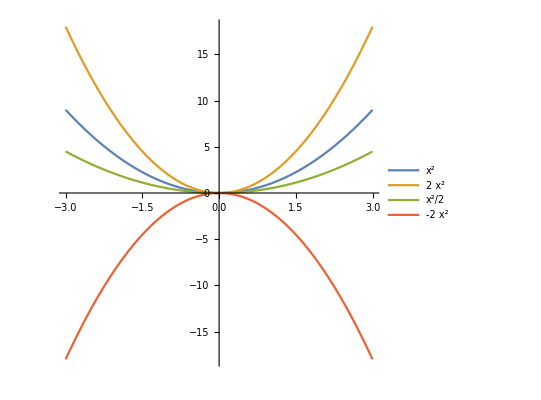

```mathematica
Plot[{x^2,2*(x)^2,1/2*(x)^2,-2*(x)^2},{x,-3,3},PlotLegends->"Expressions",AspectRatio->1]
```

Razteg po y osi.

```mathematica
Manipulate[Plot[{With[{w=(3 Sqrt[1-(x/7)^2])*a,
l=(6/7 Sqrt[10]+(3+x)/2-3/7 Sqrt[10] Sqrt[4-(x+1)^2])*a,
h=((3 (Abs[x-1/2]+Abs[x+1/2]+6)-11 (Abs[x-3/4]+Abs[x+3/4]))/2)*a,
r=(6/7 Sqrt[10]+(3-x)/2-3/7 Sqrt[10] Sqrt[4-(x-1)^2])*a},
w+(l-w) UnitStep[x+3]+(h-l) UnitStep[x+1]+(r-h) UnitStep[x-1]+(w-r) UnitStep[x-3]],(1/2 (3 Sqrt[1-(x/7)^2]+Sqrt[1-(Abs[Abs[x]-2]-1)^2]+Abs[x/2]-((3 Sqrt[33]-7)/112) x^2-3) (Sign[x+4]-Sign[x-4])-3*Sqrt[1-(x/7)^2])*a},{x,-7,7},AspectRatio->Automatic,PlotRange->{-20,20},PlotStyle->Black],{a,-6,6}]
```

y= f(x/b)
Število b s katerim delimo neodvisno spremenljivko x, pomeni razteg grafa funkcije v smeri osi x za faktor b.
Pri tem se x koordinata vsake točke na grafu pomnoži s številom b (in y koordinata ostane nespremenjena).
Razteg v smeri osi x za faktor − 1 pomeni zrcaljenje grafa funkcije čez ordinatno os.
Zgled za: f(x) = x^2

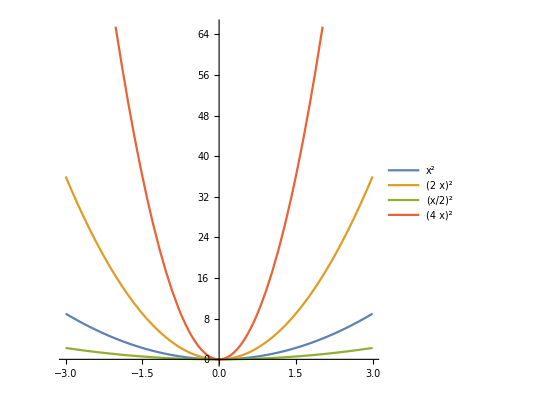

```mathematica
Plot[{x^2,(2*x)^2,(1/2*x)^2,(4*x)^2},{x,-3,3},PlotLegends->"Expressions",AspectRatio->1]
```

Razteg po x osi .

```mathematica
Manipulate[Plot[{With[{w=3 Sqrt[1-((x*b)/7)^2],
l=6/7 Sqrt[10]+(3+(x*b))/2-3/7 Sqrt[10] Sqrt[4-((x*b)+1)^2],
h=(3 (Abs[(x*b)-1/2]+Abs[(x*b)+1/2]+6)-11 (Abs[(x*b)-3/4]+Abs[(x*b)+3/4]))/2,
r=6/7 Sqrt[10]+(3-(x*b))/2-3/7 Sqrt[10] Sqrt[4-((x*b)-1)^2]},
w+(l-w) UnitStep[(x*b)+3]+(h-l) UnitStep[(x*b)+1]+(r-h) UnitStep[(x*b)-1]+(w-r) UnitStep[(x*b)-3]],1/2 (3 Sqrt[1-((x*b)/7)^2]+Sqrt[1-(Abs[Abs[(x*b)]-2]-1)^2]+Abs[(x*b)/2]-((3 Sqrt[33]-7)/112) (x*b)^2-3) (Sign[(x*b)+4]-Sign[(x*b)-4])-3*Sqrt[1-((x*b)/7)^2]},{x,-20,20},AspectRatio->Automatic,PlotRange->{{-20,20},{-5,5}},PlotStyle->Black],{b,-5,5}]
```

Še vse skupaj:

```mathematica
Manipulate[Plot[{With[{w=(3 Sqrt[1-((x*b+p)/7)^2])*a+q,
l=(6/7 Sqrt[10]+(3+(x*b+p))/2-3/7 Sqrt[10] Sqrt[4-((x*b+p)+1)^2])*a+q,
h=((3 (Abs[(x*b+p)-1/2]+Abs[(x*b+p)+1/2]+6)-11 (Abs[(x*b+p)-3/4]+Abs[(x*b+p)+3/4]))/2)*a+q,
r=(6/7 Sqrt[10]+(3-(x*b+p))/2-3/7 Sqrt[10] Sqrt[4-((x*b+p)-1)^2])*a+q},
w+(l-w) UnitStep[(x*b+p)+3]+(h-l) UnitStep[(x*b+p)+1]+(r-h) UnitStep[(x*b+p)-1]+(w-r) UnitStep[(x*b+p)-3]],(1/2 (3 Sqrt[1-((x*b+p)/7)^2]+Sqrt[1-(Abs[Abs[(x*b+p)]-2]-1)^2]+Abs[(x*b+p)/2]-((3 Sqrt[33]-7)/112) (x*b+p)^2-3) (Sign[(x*b+p)+4]-Sign[(x*b+p)-4])-3*Sqrt[1-((x*b+p)/7)^2])*a+q},{x,-20,20},AspectRatio->Automatic,PlotRange->{{-20,20},{-20,20}},PlotStyle->Black],{a,-6,6},{b,-5,5},{p,-10,10},{q,-10,10}]
```

# Viri

https : // sl.wikipedia.org/wiki/Funkcija

http : // www2.arnes.si/~mpavle1/mp/funk1.html
google(ker link ne dela): Funkcije (splošno) - Arnes

http : // www2.arnes.si/~mpavle1/mp/funk3.html
google(ker link ne dela): Risanje grafov funkcij (splošno) - Arnes